# Psoriasis modellek

[1] Fedor Shmarov, Graham R. Smith, Sophie C. Weatherhead, Nick J. Reynolds and  Paolo Zuliani (2022). Individualised computational modelling of immune mediated disease onset, flare and clearance in psoriasis. (JPLOS Computationay Biology)

## Paraméterek

A szimulációkat differenciálegyenlet-rendszerek megoldásával végezzük. Az egyenletek paramétereit és a kezdeti értékeket változtatjuk, hogy vizsgáljuk a rendszer működését különböző esetekben. Ezért ezeket előre eltároljuk, és később mindig csak a megfelelő paramétereket változtatjuk.

```mathematica
primaryParameters=<|sc2->0.0017635,
sc20->1.8135 ×10^-5,
sc2ta->0.0015415,
sc2gf->1,
ta2->0.0017562,
ta20->3.7321×10^-6,
ta2d->0.0018063,
ta2gf->1,
d20->5.05×10^-7,
dDesq->0.0047529,
dc20->1.51,
dcVm->6000,
dcKp->3×10^12,
il172->0.5,
il1720->36.5,
t2->55,
t20->1.51,
gf20->36.5,
aBase->0.0036,
a20->36,
tnf2->0.5,
tnf20->36.5,
il232->1,
il2320->36.5,
p->2,
n->4,
dcAct->1880|>;
```

```mathematica
initialConditionsHealthy=<|sc0->5000,ta0->29000,dk0->64000,t0->700,dc0->700,a0->2,il170->20,il230->40,tnf0->20,gf0->700|>;
```

### Paraméterek jelentése

-Graphics-

## Reynolds-modell vizsgálata

## Egyenletrendszer (Reynolds-modell)

A Reynolds-féle cikkből [1] ismert egyenletrendszert először változtatás nélkül implementáljuk. A kezdeti értékekhez tartozó egyenleteket is eltároljuk, később ezt a kettőt a megoldáshoz egyesítjük. Ezen kívül ebben a fejezetben van egy egyenletrendszer megoldó és egy ábrázoló függvény.

```mathematica
reynoldsDefaultEqns={SC'[t]==sc2*(IL17⎵22[t]+TNF[t])*SC[t]-sc20*(SC[t])^p-aBase*SC[t],TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta*SC[t]+ta2*TA[t])-ta20*(TA[t])^p-aBase*TA[t],
DK'[t]==ta2d*(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase*DK[t]-dDesq*DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcAct-dc20*DC[t]-aBase*DC[t],
IL17⎵22'[t]== il172*T[t]-il1720*IL17⎵22[t],
T'[t]== t2*IL23[t]-t20*T[t]-aBase*T[t],
GF'[t]== sc2gf*SC[t]+ta2gf*TA[t]-gf20*GF[t],
A'[t]== aBase*(SC[t]+TA[t]+DC[t]+T[t]+DK[t])-a20*A[t],
TNF'[t]== tnf2*T[t]-tnf20*TNF[t],
IL23'[t]== il232*DC[t]-il2320*IL23[t]};
```

```mathematica
setInitialCondition=
{SC[0]==sc0,
TA[0]==ta0,
DK[0]==dk0,
T[0]==t0,
DC[0]==dc0,
A[0]==a0,
IL17⎵22[0]==il170,
IL23[0]==il230,
TNF[0]==tnf0,
GF[0]==gf0};
```

```mathematica
solveReynoldsDefault[parameterList_,conditionList_]:=First[NDSolve[
Join[reynoldsDefaultEqns/.parameterList, setInitialCondition/.conditionList],{SC,TA,DK,DC,IL17⎵22,T,GF,A,TNF,IL23},{t,0,1000}]];
```

```mathematica
visualizer[solution_]:= Plot[Evaluate[{SC[t],TA[t],DK[t]}/. solution],{t,0,1000},PlotStyle->{{RGBColor[0.937,0.431,0.008],Thickness[.006]},{RGBColor[0.5,0,0.5],Thickness[.006]},{RGBColor[0.25,0.87,0.81],Thickness[.006]}},ImageSize->Scaled[0.5],
PlotLabel->"Number of keratinocytes", LabelStyle->Directive[Black,FontSize->15],
PlotLegends->{"stemcells","tranzit-amplifying","differenciating ker."},PlotRange->All];
```

## DcAct vizsgálat

A betegséget “beindító” immunológiai inger az egyenletrendszerben egy dcAct tag, amely a dendritikus sejtek egyenletében szerepel. Azt feltételezzük, hogy ennek fontos szerepe van a modellben, ezért a viselkedését vizsgáljuk három állapotban.
- Egészséges kezdeti értékek, alacsony dcAct: Ez annak felel meg, hogy a bőrsejtek száma normális, és a bőrt nem érte semmilyen inger.
- Egészséges kezdeti értékek, magas dcAct: Ez annak felel meg, hogy a bőrsejtek száma normális, de valamilyen trigger (pl. sérülés) érte a rendszert.
- Magas kezdeti értékek, alacsony dcAct: Ez annak felel meg, hogy a betegség beindult és a bőrben a sejtek száma kórosan magas, de a trigger megszűnt.
Azt szeretnénk látni, hogy a betegség beindulása után az inger megléte nélkül is fennáll a betegség.

Kíváncsiságból kirajzoltatom a DC és a GF görbéket is, mivel a DC egyenlete érdekes.

```mathematica
dcVisualizer[solution_]:=Plot[Evaluate[{DC[t],GF[t]}/.solution],{t,0,300},PlotStyle->Thickness[.006], PlotRange->All]
```

Egészséges kezdeti értékek, alacsony dcAct

Ebben az esetben azt látjuk, hogy a megoldásgörbék egy alacsony egyensúlyi állapotnál állnak be, ez az egészséges egyensúlyi helyzet (később számoljuk)

```mathematica
healthyInitLowDcActSol=solveReynoldsDefault[primaryParameters,initialConditionsHealthy];
```

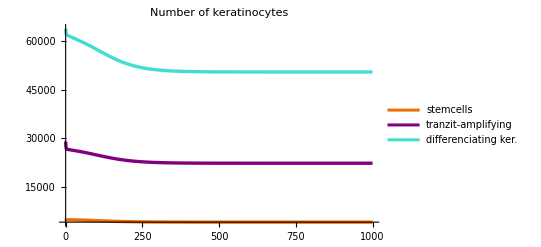

```mathematica
visualizer[healthyInitLowDcActSol]
```

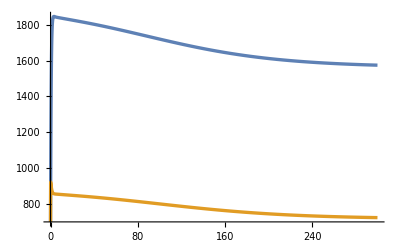

```mathematica
dcVisualizer[healthyInitLowDcActSol]
```

Egészséges kezdeti értékek, magas dcAct

A dcAct-ot 2%-kal megemeltük. Ekkor látjuk a görbéken, hogy egy magas, feltehetően beteg egyensúlyi helyzethez tartanak, tehát kialakul a betegség.

```mathematica
highDcActParameters=Append[primaryParameters, dcAct->1880*1.02]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1917.6|>

```mathematica
healthyInitHighDcActSol=solveReynoldsDefault[highDcActParameters,initialConditionsHealthy];
```

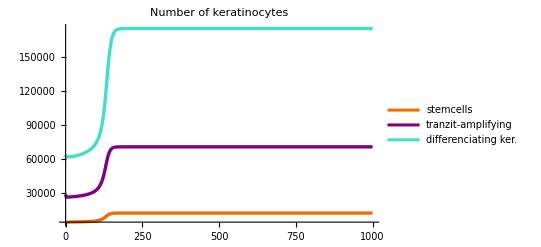

```mathematica
visualizer[healthyInitHighDcActSol]
```

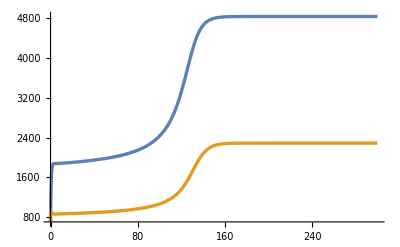

```mathematica
dcVisualizer[healthyInitHighDcActSol]
```

Magas kezdeti értékek, alacsony dcAct

Itt megemelkedett, azaz nem egészséges kezdeti értékekkel, de visszacsökkentett dcActtal ábrázolunk. Azt látjuk, hogy ebben az esetben a is kialakul, visszatér a betegség.

```mathematica
initialConditionsPsori=<|sc0->6000,ta0->35000,dk0->80000,t0->2300,dc0->2300,a0->6,il170->60,il230->40,tnf0->60,gf0->2100|>;
```

```mathematica
psoriInitLowDcActSol=solveReynoldsDefault[primaryParameters,initialConditionsPsori];
```

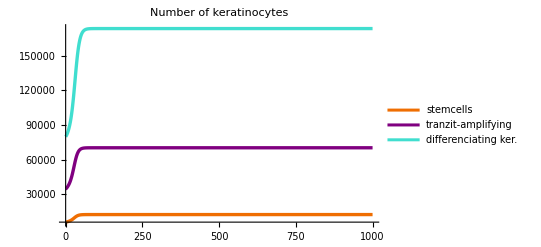

```mathematica
visualizer[psoriInitLowDcActSol]
```

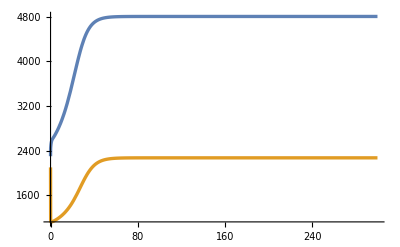

```mathematica
dcVisualizer[psoriInitLowDcActSol]
```

## Reynolds-modell újradefiniálása (WhenEvent használat, IL17/22 gátló gyógyszer)

Újradefiniáljuk a Reynolds-modellt a következő módon: 
- Nem realisztikus, hogy egy immunológiai inger a megjelenés után “örökre” fennmarad (pl. egy sérülés esetében meggyógyulunk). Ezt a modellben úgy szemléltetjük, hogy a dcAct-ot csak egy időintervallumon belül emeljük meg/stimuláljuk, aztán visszaáll az eredeti értékére.
Ezért a kezdeti értékek közé is eltároltunk egy dcAct0 értéket. Ez az általunk megadott mértékben növeli (stimulálja) a dcActot, majd t=100-nál 1880-ra (eredeti érték) vált.
- Meg akarjuk nézni mi történik ha visszafogjuk a citokin termelődést (egyfajta kezelésként). Erre azért vagyunk kíváncsiak, mert a később bevezetni kívánt memóriasejtek is az IL17/22 termelésébe szállnak be. Ehhez bevezettünk egy il1722Red paramétert, ami egy bizonyos időben blokkolja az IL17/22-t. Az időt az alapján választottam meg, hogy a korábbi vizsgálatnál mikorra alakult már ki a betegség. Ezért a paraméterek közé bekerül az il1722RedLater (IL17/22 reduction that we only give later).

### Új paraméterek, egyenletrendszer, megoldófüggvény

```mathematica
initialCondsStimulated=Append[initialConditionsHealthy,dcAct0->1880*1.02]
```

<|sc0→5000,ta0→29000,dk0→64000,t0→700,dc0→700,a0→2,il170→20,il230→40,tnf0→20,gf0→700,dcAct0→1917.6|>

```mathematica
stimulatedParameters=Append[primaryParameters, il1722RedLater->1]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1|>

```mathematica
reynoldsStimulatedEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20*(SC[t])^p-aBase *SC[t],TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta *SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase *DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20 *DC[t]-aBase *DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*T[t]-il1720* IL17⎵22[t],
T'[t]== t2 *IL23[t]-t20* T[t]-aBase* T[t],
GF'[t]== sc2gf* SC[t]+ta2gf *TA[t]-gf20* GF[t],
A'[t]== aBase *(SC[t]+TA[t]+DC[t]+T[t]+DK[t])-a20* A[t],
TNF'[t]== tnf2* T[t]-tnf20*TNF[t],
IL23'[t]== il232 *DC[t]-il2320 *IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 400, {il1722Red[t] -> il1722RedLater}]};
```

```mathematica
setInitialCondsStimulated=
{SC[0]==sc0,
TA[0]==ta0,
DK[0]==dk0,
T[0]==t0,
DC[0]==dc0,
A[0]==a0,
IL17⎵22[0]==il170,
IL23[0]==il230,
TNF[0]==tnf0,
GF[0]==gf0,
dcActFunction[0]==dcAct0,
il1722Red[0]==1};
```

```mathematica
solveReynoldsStimulated[parameterListR_,conditionListR_]:=First[NDSolve[
Join[reynoldsStimulatedEqns/.parameterListR, setInitialCondsStimulated/.conditionListR],{SC,TA,DK,DC,IL17⎵22,T,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,1000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

### Szimulációk

Megpróbáljuk a korábban látott “beteg” állapotot elérni: dcAct emelése citokinráta változtatása nélkül. A görbék ugyanúgy beállnak a beteg egyensúlyi helyzet közelébe, viszont fontos megjegyezni, hogy itt az ingert csak 100 időegységig tartottuk fenn, a betegség mégis beállt.

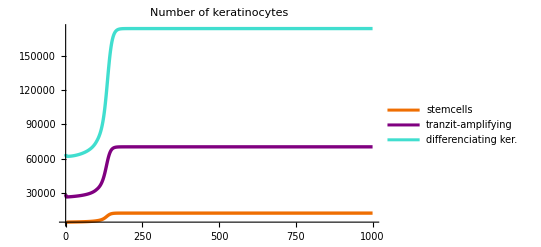

```mathematica
highDcActNoReductionSol=solveReynoldsStimulated[stimulatedParameters, initialCondsStimulated];
visualizer[highDcActNoReductionSol]
```

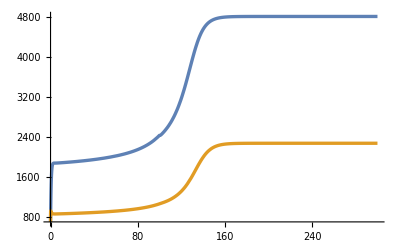

```mathematica
dcVisualizer[highDcActNoReductionSol]
```

Most, hogy a betegség megjelent, próbáljuk meg a “citokingátló gyógyszer” használatát, az il1722RedLater csökkentésével, és vizsgáljuk a viselkedést.

10%-os blokklás:

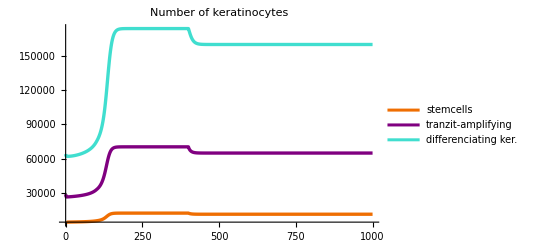

```mathematica
highDcActWithReduction90Sol=solveReynoldsStimulated[Append[stimulatedParameters,il1722RedLater->0.9],initialCondsStimulated];
visualizer[highDcActWithReduction90Sol]
```

20%-os blokkolás

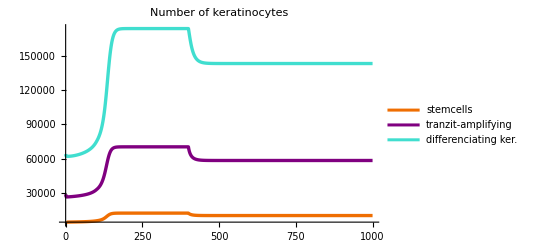

```mathematica
highDcActWithReduction80Sol=solveReynoldsStimulated[Append[stimulatedParameters,il1722RedLater->0.8],initialCondsStimulated];
visualizer[highDcActWithReduction80Sol]
```

30%-os blokkolás

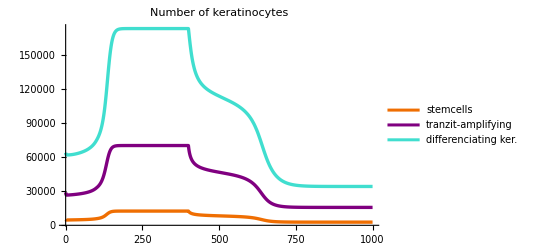

```mathematica
highDcActWithReduction70Sol=solveReynoldsStimulated[Append[stimulatedParameters,il1722RedLater->0.7],initialCondsStimulated];
visualizer[highDcActWithReduction70Sol]
```

## Egyensúlyi helyzetek

Kiszámoljuk az egyensúlyi helyzeteket az eredeti paraméterekkel, és összehasonlítjuk az eredményeinket az [1]-ben szereplő ereményekkel.

```mathematica
steadyStates=Solve[
{0==sc2 *(IL17⎵22+TNF)*SC-sc20 *(SC)^p-aBase*SC,
0==(IL17⎵22+TNF)*(sc2ta*SC+ta2*TA)-ta20*(TA)^p-aBase*TA,
0==ta2d*(IL17⎵22+TNF)*TA-d20 *(DK)^p-aBase*DK-dDesq*DK,
0== (dcVm*(GF)^n)/(dcKp+(GF)^n)+dcAct-dc20*DC-aBase*DC,
0== il172*T-il1720*IL17⎵22,
0== t2*IL23-t20*T-aBase*T,
0== sc2gf*SC+ta2gf*TA-gf20*GF,
0== aBase *(SC+TA+DC+T+DK)-a20*A,
0== tnf2*T-tnf20*TNF,
0== il232*DC-il2320*IL23}/.primaryParameters,{SC,TA,DK,DC,IL17⎵22,T,GF,A,TNF,IL23}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Összes egyensúlyi helyzetek szám:

```mathematica
Length[steadyStates]
```

32

Ezek közül a valós, pozitív egyensúlyi helyzetek:

```mathematica
realSteady=Association/@(Select[steadyStates,FreeQ[{SC,TA,DK}/. #,Complex[_,_]]&&  And@@(Positive/@{SC,TA,DK}/. #)&]);
steadyKeratinocytes=KeyTake[#,{SC,TA,DK}]&/@realSteady
```

{<|SC→3947.21,TA→22224.4,DK→50529.4|>,<|SC→4855.46,TA→27308.7,DK→63458.5|>,<|SC→12544.2,TA→70349.6,DK→173504.|>}

```mathematica
realSteady
```

{<|SC→3947.21,TA→22224.4,DK→50529.4,DC→1563.06,IL17⎵22→21.3163,T→1556.09,GF→717.03,A→7.98201,TNF→21.3163,IL23→42.8237|>,<|SC→4855.46,TA→27308.7,DK→63458.5,DC→1905.5,IL17⎵22→25.9863,T→1897.,GF→881.21,A→9.94252,TNF→25.9863,IL23→52.2055|>,<|SC→12544.2,TA→70349.6,DK→173504.,DC→4804.4,IL17⎵22→65.5201,T→4782.97,GF→2271.06,A→26.5985,TNF→65.5201,IL23→131.627|>}

Az ”egészséges” egyensúlyi helyzeteket összehasonlítjuk a cikkbeliekkel:

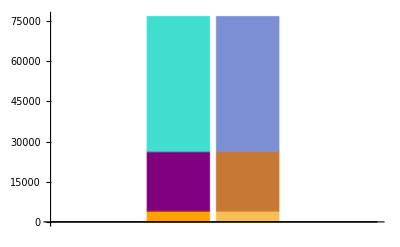

```mathematica
BarChart[{{SC,TA,DK}/.steadyKeratinocytes[[1]],{Style[3947.21,RGBColor[0.98,0.75,0.33]],Style[22224.37,RGBColor[0.78,0.47,0.2]],Style[50529.36,RGBColor[0.49,0.56,0.83]]}}, ChartLayout->"Stacked",ChartStyle->{{RGBColor[1,0.64,0],RGBColor[0.5,0,0.5],RGBColor[0.25,0.87,0.81]}}]
```

Az összes egyensúlyi helyzet keratinocitái oszlopdiagramon ábrázolva:

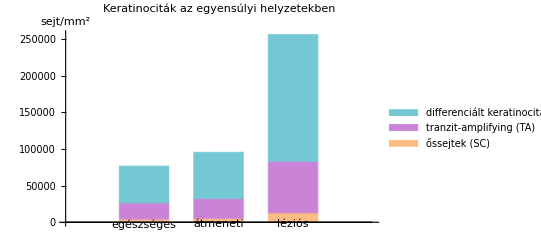

```mathematica
BarChart[{Labeled[{SC,TA,DK}/.steadyKeratinocytes[[1]],"egészséges"],Labeled[{SC,TA,DK}/.steadyKeratinocytes[[2]],"átmeneti"],Labeled[{SC,TA,DK}/.steadyKeratinocytes[[3]],"léziós"]},BarSpacing->0.5, ChartLayout->"Stacked",ChartStyle->{{RGBColor[0.996,0.737,0.522],RGBColor[0.788,0.518,0.843],RGBColor[0.451,0.784,0.831]}},ChartLegends->{"őssejtek (SC)","tranzit-amplifying (TA)", "differenciált keratinociták (K)"},AxesLabel->"sejt/mm^2",PlotLabel->"Keratinociták az egyensúlyi helyzetekben", LabelStyle->Directive[Black,FontSize->12]]
```

## Linearizálás, egyensúlyi helyzetek stabilitása, Manipulate

A három egyensúlyi helyzet a cikk szerint az egészséges, transition és a beteg egyensúlyi helyzet. Ezek közül a transition instabil, a másik kettő stabil.
Először ellenőrizni szeretnénk, hogy valóban ez a stabilitás a mi számolásunkkal is, majd ki szeretnénk próbálni, hogy paraméterek változtatásával kibillenthetjük-e a stabilitást. 
Az ötlet az, hogy ha valamelyik paraméter változtatásával a beteg, stabil egyensúlyi helyzet instabillá válik, vagy eltűnik, akkor ezt egyfajta “gyógyításnak” vagy kezelésnek tekinthetjük. 
Matematikailag egy egyensúlyi helyzet akkor stabil, ha a hozzá tartozó Jacobi-mátrix minden sajátértékének valós része negatív, különben instabil. Így ebben a fejezetben először Jacobi-mátrixot számolunk (deriválással), majd ebbe helyettesítjük be a paramétereket, és a vizsgált egyensúlyi helyzeteket.
Aztán a Manipulate segítségével változtatunk egy, vagy több paraméter értékén, miközben vizsgáljuk a sajátértékek viselkedését.

### Jacobi mátrix

```mathematica
toDifferentiate={sc2*(IL17⎵22+TNF)*SC-sc20*(SC)^p-aBase*SC,
(IL17⎵22+TNF)*(sc2ta*SC+ta2*TA)-ta20*(TA)^p-aBase*TA,
ta2d*(IL17⎵22+TNF)*TA-d20 *(DK)^p-aBase*DK-dDesq*DK,
 (dcVm*(GF)^n)/(dcKp+(GF)^n)+dcAct-dc20*DC-aBase*DC,
 il172*T-il1720*IL17⎵22,
 t2*IL23-t20*T-aBase*T,
 sc2gf*SC+ta2gf*TA-gf20*GF,
 aBase*(SC+TA+DC+T+DK)-a20*A,
 tnf2*T-tnf20*TNF,
 il232*DC-il2320*IL23};
```

```mathematica
jacobiReynolds=First[D[{toDifferentiate}, {{SC, TA, DK, DC, IL17⎵22, T, GF, A, TNF, IL23}}] ];
```

Jacobi-mátrix szimolikus alakban:

```mathematica
jacobiReynolds//MatrixForm
```

(-aBase-p SC^(-1+p) sc20+sc2 (IL17⎵22+TNF) | 0 | 0 | 0 | SC sc2 | 0 | 0 | 0 | SC sc2 | 0
sc2ta (IL17⎵22+TNF) | -aBase-p TA^(-1+p) ta20+ta2 (IL17⎵22+TNF) | 0 | 0 | SC sc2ta+TA ta2 | 0 | 0 | 0 | SC sc2ta+TA ta2 | 0
0 | ta2d (IL17⎵22+TNF) | -aBase-dDesq-d20 DK^(-1+p) p | 0 | TA ta2d | 0 | 0 | 0 | TA ta2d | 0
0 | 0 | 0 | -aBase-dc20 | 0 | 0 | -(dcVm GF^(-1+2 n) n)/((dcKp+GF^n)^2)+(dcVm GF^(-1+n) n)/(dcKp+GF^n) | 0 | 0 | 0
0 | 0 | 0 | 0 | -il1720 | il172 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -aBase-t20 | 0 | 0 | 0 | t2
sc2gf | ta2gf | 0 | 0 | 0 | 0 | -gf20 | 0 | 0 | 0
aBase | aBase | aBase | aBase | 0 | aBase | 0 | -a20 | 0 | 0
0 | 0 | 0 | 0 | 0 | tnf2 | 0 | 0 | -tnf20 | 0
0 | 0 | 0 | il232 | 0 | 0 | 0 | 0 | 0 | -il2320)

### Egyensúlyi helyzetek

Itt paraméteresen kiszámoljuk az egyensúlyi helyzeteket, hogy később tetszőleges paramétereket megadhassunk neki.

```mathematica
changableSteadyStatesEqns[params_]:=Solve[
{0==sc2 *(IL17⎵22+TNF)*SC-sc20 *(SC)^p-aBase*SC,
0==(IL17⎵22+TNF)*(sc2ta*SC+ta2*TA)-ta20*(TA)^p-aBase*TA,
0==ta2d*(IL17⎵22+TNF)*TA-d20 *(DK)^p-aBase*DK-dDesq*DK,
0== (dcVm*(GF)^n)/(dcKp+(GF)^n)+dcAct-dc20*DC-aBase*DC,
0== il172*T-il1720*IL17⎵22,
0== t2*IL23-t20*T-aBase*T,
0== sc2gf*SC+ta2gf*TA-gf20*GF,
0== aBase *(SC+TA+DC+T+DK)-a20*A,
0== tnf2*T-tnf20*TNF,
0== il232*DC-il2320*IL23}/.params,{SC,TA,DK,DC,IL17⎵22,T,GF,A,TNF,IL23}];
```

```mathematica
realSteadyStates[steadyStateList_]:=Association/@(Select[steadyStateList,FreeQ[{SC,TA,DK}/. #,Complex[_,_]]&&  And@@(Positive/@{SC,TA,DK}/. #)&]);
```

Tehát változtatható paraméterekkel kiszámolódik az összes egyensúlyi helyzet, majd ebből kiválasztódnak a valósak.
Például az alap paraméterekkel visszakapjuk a korábban látott egyensúlyi helyzeteket:

```mathematica
realSteadyStates[changableSteadyStatesEqns[primaryParameters]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{<|SC→3947.21,TA→22224.4,DK→50529.4,DC→1563.06,IL17⎵22→21.3163,T→1556.09,GF→717.03,A→7.98201,TNF→21.3163,IL23→42.8237|>,<|SC→4855.46,TA→27308.7,DK→63458.5,DC→1905.5,IL17⎵22→25.9863,T→1897.,GF→881.21,A→9.94252,TNF→25.9863,IL23→52.2055|>,<|SC→12544.2,TA→70349.6,DK→173504.,DC→4804.4,IL17⎵22→65.5201,T→4782.97,GF→2271.06,A→26.5985,TNF→65.5201,IL23→131.627|>}

Ezek Association-ként tárolódnak, így könnyen behelyettesíthetők a Jacobi mátrixba. A sajátértékek számolásához a Jacobi mátrixba helyettesítjük a paramétereket, és egyenként a valós egyensúlyi helyzeteket, így számmátrixokat kapunk.

```mathematica
healthyJacobi[parameterList_, steadyStateList_]:=jacobiReynolds/.parameterList/.steadyStateList[[1]];
transitionJacobi[parameterList_, steadyStateList_]:=jacobiReynolds/.parameterList/.steadyStateList[[2]];
psoriJacobi[parameterList_, steadyStateList_]:=jacobiReynolds/.parameterList/.steadyStateList[[3]];
```

Ha minden sajátérték valós része negatív, akkor stabil a mátrixhoz tartozó egyensúlyi helyzet, különben instabil.

```mathematica
stability[eigenvalues_]:=If[Negative[Re[eigenvalues]]=={True,True,True,True,True,True,True,True,True,True},
"stabil","instabil"]
```

Példa: az eredeti paraméterekkel, a beteg egyensúlyi helyzet sajátértékei:

```mathematica
psoriEigenvalueExample=Eigenvalues[psoriJacobi[primaryParameters,realSteadyStates[changableSteadyStatesEqns[primaryParameters]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-37.0725+0. ⅈ,-36.5+0. ⅈ,-36.2142+0.512105 ⅈ,-36.2142-0.512105 ⅈ,-36.+0. ⅈ,-1.56306+0.385426 ⅈ,-1.56306-0.385426 ⅈ,-0.273714+0. ⅈ,-0.183592+0. ⅈ,-0.152476+0. ⅈ}

```mathematica
stability[psoriEigenvalueExample]
```

stabil

### Manipulate

A Solve jelzését itt kikapcsoljuk.

```mathematica
Off[Solve::ratnz];
```

A sajátértékek mint komplex számok és az egyensúlyi helyzetek lesznek ábrázolva, hogy lássuk a mozgást a paraméterek változtatására. Ehhez ábrázoló függvények vannak. 
Mivel a paraméterek változtatásával megszűnhetnek valós (ez csak annyit tesz, hogy nem valóssá válik) egyensúlyi helyzetek, ezért a függvények úgy vannak írva, hogy csak annyit ábrázol amennyi létezik.
Megjegyzés: Az ábrázoló függvények a jelmagyarázatot sorrendben írják ki, nem értékhez kötve, így ha eltűnik egyensúlyi helyzet, a megmaradtak a jelmagyarázatot a sor elejéről kapják. Megtévesztő lehet, de előfordulhat, hogy a megmaradó egyensúlyi helyzet beteg, bár a “healthy” jelmagyarázat van rajta. Eltűnés esetén az értékre figyeljünk, ne a jelmagyarázatra.

```mathematica
eigenvalueVisualizer[points_]:=ComplexListPlot[Take[points,UpTo[3]],PlotRange->0.1,PlotLegends->PointLegend[{"healthy","transition","psoriatic"}],PlotLabel->"Eigenvalues",PlotMarkers->Automatic];
ticks={{1,"SC"},{2,"TA"},{3,"DK"}};
stadyStateVisualizer[ss_]:=ListPlot[MapThread[Labeled[#1,#2]&,{Map[If[KeyExistsQ[#,SC]&&KeyExistsQ[#,TA]&&KeyExistsQ[#,DK],{#[SC],#[TA],#[DK]},Nothing]&,Take[ss,UpTo[3]]],{"healthy","transition","psoriatic"}[[;;Length[ss]]]}],Ticks->{ticks,Automatic},PlotLabel->"Steady States",PlotMarkers->Automatic];
```

#### A paraméterek amiket változtatunk:

```mathematica
primaryParameters
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880|>

-Graphics-

#### A paraméterek változtatása

Mindegyiket kipróbáltam és leírtam amit láttam, majd az output-okat kivettem, mert nagyon lelassította.

A Manipulatehez az il172 (az IL17/22 termelődési rátája T szerint), a t2 (a T aktiválódási rátája az IL23 szerint) és a tnf2 (a TNF termelődési rátája T szerint) paramétereket találtam érdekesnek kipróbálni, mert ezek az immunrendszer elemeinek (T-sejtek, citokinek) a termelődési rátái. (már 3 paraméterrel is elég lassú)

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},parameterList=Append[primaryParameters,{il172->x,t2->y,tnf2->z}];eqs=realSteadyStates[changableSteadyStatesEqns[parameterList]];eigenvals=(Eigenvalues[jacobiReynolds/.parameterList/.#1]&)/@eqs;Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],{{x,0.5},0.1,1,0.001,Appearance->"Labeled"},{{y,55},45,60,0.1,Appearance->"Labeled"},{{z,0.5},0.1,1,0.01,Appearance->"Labeled"}];
```

A paraméterek csökkentésével a transition és psoriatic állapot csúszik össze, a növeléssel a transition és healthy.

Keratinociták: sc2, sc20, sc2ta, ta2, ta20, ta2d, d20, ddesq, p

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{sc2->x, sc20->y,p->z}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,0.0017635},0,0.0025,Appearance->"Labeled"},{{y,1.8135 ×10^-5},0,2.5 ×10^-5,Appearance->"Labeled"},
{{z,2},1,3,1,Appearance->"Labeled"}];
```

Az sc2, sc20 változtatásával ugyanaz a viselkedés. A p változtatására nagyon érzékeny a rendszer (ez hatványkitevő az egyenletrendszeben).

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{ta2->x, ta20->y,sc2ta->z}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,0.0017562},0,0.0025,Appearance->"Labeled"},{{y,3.7321×10^-6},3×10^-6,4.7 ×10^-6,Appearance->"Labeled"},
{{z,0.0015415},0,0.0025,Appearance->"Labeled"}];
```

A ta2, ta20 változtatásával ugyanaz a viselkedés, viszont az sc2ta csökkentése nem sokat befolyásol, még ha 0-ra állítjuk is megmarad mind a három egyensúlyi helyzet.

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{ta2d->x, d20->y,dDesq->z}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,0.0018063},0,0.005,Appearance->"Labeled"},{{y,5.05×10^-7},0,10^-6,Appearance->"Labeled"},
{{z,0.0047529},0.003,0.0055,Appearance->"Labeled"}];
```

A ta2d csökkentésével a TA egyensúlyi helyzetei nagyobbak lesznek mint a D egyensúlyi helyzetei (a D csökken), de egyensúlyi helyzet nem tűnik el (a növelésével sem). A d20 változtatásával az egyensúlyi helyzetek értéke változik, de a stabilitásuk nem. A ddesq változtatása nem befolyásolja látványosan az egyensúlyi helyzeteket. (A D egyébként már nem vesz részt a körforgásban, így érthető, hogy nem nagyon befolyásol.)

DC paraméterei: dcVm, dcKp, dcAct, dc20, n

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{dcVm->x, dcKp->y,dc20->z}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,6000},4000,7000,Appearance->"Labeled"},{{y,3×10^12},2.5×10^12,6×10^12,Appearance->"Labeled"},
{{z,1.51},1,2,Appearance->"Labeled"}];
```

A dcVm emelésre érzékenyebb, mint csökkentésre, a dcKp csökkentésre érzékenyebb. De mindhárom paraméter változtatásával a korábbi viselkedést kapjuk.

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{dcAct->x, n->y}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,1880},1000,1950,Appearance->"Labeled"},{{y,4},1,6,1,Appearance->"Labeled"}];
```

A dcAct emelésre nagyon érzékeny, az n hatványkitevő változtatásával azonnal “eltűnik” 2 egyensúlyi helyzet.

Citokinek és T-sejt: il1720, tnf20, t20, il232, il2320 (il172, tnf2, t2 korábban)

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{il1720->x, t20->y,tnf20->z}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,36.5},30,55,Appearance->"Labeled"},{{y,1.51},1,2,Appearance->"Labeled"},
{{z,36.5},30,55,Appearance->"Labeled"}];
```

A paraméterek növelésével a transition és psoriatic állapot csúszik össze, a csökkentéssel a transition és healthy.

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{il232->x, il2320->y}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,1},0.8,1.1,Appearance->"Labeled"},{{y,36.5},30,55,Appearance->"Labeled"}];
```

Az il232 nagyon érzékeny.

GF és A: sc2gf, ta2gf, gf20, aBase, a20

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{sc2gf->x, ta2gf->y,gf20->z}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,1},0,1.5,Appearance->"Labeled"},{{y,1},0.8,1.7,Appearance->"Labeled"},
{{z,36.5},35,45,Appearance->"Labeled"}];
```

A ta2gf sokkal érzékenyebb mint az sc2gf. A gf20 csökkentésre nagyon érzékeny.

```mathematica
Manipulate[Module[{parameterList,eqs,eigenvals},
parameterList=Append[primaryParameters,{aBase->x, a20->y}];
eqs = realSteadyStates[changableSteadyStates[parameterList]];
eigenvals= Map[Eigenvalues[jacobiReynolds/.parameterList /. #]&,eqs];
Column[{GraphicsRow[{eigenvalueVisualizer[eigenvals],
stadyStateVisualizer[eqs]},ImageSize->Full],"Sajátértékek:",eigenvals,"Egyensúlyi helyzetek:",eqs}]],
{{x,0.0036},0,0.03,Appearance->"Labeled"},{{y,36},30,55,Appearance->"Labeled"}];
```

Az aBase csökkentésével összecsúszik a healthy és a transition,  a növelésével a psori és a transition. Az a20 nem nagyon befolyásol.

A fellépő bifurkáció magyarázata: hiányzik

## TRM-modell

## Reynolds-modell kibővítése memória T-sejtekkel (több lépésben)

A modellt szeretnénk bővíteni a tissue resident memory T-sejtek bevételével. Először egy 0. lépésként csak hozzáadjuk az új egyenletet, úgy, hogy a TRM hatása ugyanaz legyen mint a T-sejtek hatása. Ez egyfajta “sanity check”, ebben a lépésben lényegében szétválasztjuk a korábbi T-sejteket két részre. A cél az, hogy az ezzel elvégzett szimuláció ugyanazt adja vissza mint a korábbi. Ezt a verziót később nem fogjuk használni.
Ha ez működik, akkor figyelembe véve a TRM sejtek általunk ismert tulajdonságait, több lépésben implementáljuk őket.
A T <->TRM átmenet egyelőre egy egyszerű +/- taggal és t2trm (t->trm), trm2t (trm->t) paraméterekkel van megoldva.
“Tehát psoriasisban 50% körüli TRM/T sejt aránnyal kell számolnunk, az epidermisben.” -> Azt szeretnénk elérni, hogy az új modellben a T és TRM sejtek száma megegyezzen. Ehhez írunk egy ábrázolófüggvény, hogy minden szimuláció esetében megnézhessük a T és TRM göbéket is.

```mathematica
tCellVisualizer[solution_]:=Plot[Evaluate[{T[t], TRM[t]}/. solution],{t,0,1000},PlotStyle->{{RGBColor[0.4,0.8,0],Thickness[.006]},{RGBColor[1,0,0.49],Thickness[.005]}}, ImageSize->Scaled[0.5],LabelStyle->Directive[Black,FontSize->15],PlotLegends->{"T","TRM"},PlotRange->All,PlotLabel->"Immune-cells"];
```

```mathematica
trmVisualizer[solution_]:=Grid[{{Plot[Evaluate[{SC[t],TA[t],DK[t]}/. solution],{t,0,300},PlotStyle->{{RGBColor[1,0.64,0],Thickness[.006]},{RGBColor[0.5,0,0.5],Thickness[.006]},{RGBColor[0.25,0.87,0.81],Thickness[.006]}},ImageSize->Scaled[0.5],
PlotLabel->"Optimized TRM", LabelStyle->Directive[Black,FontSize->15],
(*PlotLegends->{"stemcells","tranzit-amplifying","differenciating ker."},*)PlotRange->All],Plot[Evaluate[{T[t],TRM[t]}/. solution],{t,0,300},PlotStyle->{{RGBColor[0.4,0.8,0],Thickness[.008]},{RGBColor[1,0,0.49],Thickness[.006], Dashed}},ImageSize->Scaled[0.5],
PlotLabel->"Optimized TRM", LabelStyle->Directive[Black,FontSize->15],
(*PlotLegends->{"t-cells","trm"},*)PlotRange->{0,5000}]},{SpanFromLeft,SwatchLegend[{RGBColor[1,0.64,0],RGBColor[0.5,0,0.5],RGBColor[0.25,0.87,0.81],RGBColor[0.4,0.8,0],RGBColor[1,0,0.49]},{"stemcells","tranzit-amplifying","differenciating ker.","t-cells","trm"}]}},Spacings->{2,2}]
```

#### 0. TRM úgy viselkedik mint a T

Ez egy ellenőrző lépés, hogy visszakapjuk-e ugyanazokat az eredményeket, ha a TRM ugyanarra hat, mint a T. Ábrázoljuk a T, TRM görbéket is, hogy megnézzük mennyi van a sejtekből ebben az esetben.

```mathematica
parametersTRM=Append[stimulatedParameters, {t2trm->0.2,trm2t->0.002}]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,t2trm→0.2,trm2t→0.002|>

```mathematica
initialCondsWithTRM=Append[initialCondsStimulated,{trm0->140,t0->560}]
```

<|sc0→5000,ta0→29000,dk0→64000,dc0→700,a0→2,il170→20,il230→40,tnf0→20,gf0→700,dcAct0→1917.6,trm0→140,t0→560|>

```mathematica
reynoldsWithTRMEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20*(SC[t])^p-aBase *SC[t],TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta *SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase *DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20 *DC[t]-aBase *DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*(T[t]+TRM[t])-il1720* IL17⎵22[t],
T'[t]== t2 *IL23[t]+trm2t*TRM[t]-t2trm *T[t]-t20* T[t]-aBase* T[t],
TRM'[t]==t2trm*T[t]-trm2t*TRM[t]-t20*TRM[t]-aBase *TRM[t],
GF'[t]== sc2gf* SC[t]+ta2gf *TA[t]-gf20* GF[t],
A'[t]== aBase *(SC[t]+TA[t]+DC[t]+T[t]+TRM[t]+DK[t])-a20* A[t],
TNF'[t]== tnf2* (T[t]+TRM[t])-tnf20*TNF[t],
IL23'[t]== il232 *DC[t]-il2320 *IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 400, {il1722Red[t] -> il1722RedLater}]};
```

```mathematica
setInitialCondsWithTRM=
{SC[0]==sc0,
TA[0]==ta0,
DK[0]==dk0,
T[0]==t0,
TRM[0]==trm0,
DC[0]==dc0,
A[0]==a0,
IL17⎵22[0]==il170,
IL23[0]==il230,
TNF[0]==tnf0,
GF[0]==gf0,
dcActFunction[0]==dcAct0,
il1722Red[0]==1};
```

```mathematica
solveReynoldsWithTRM[parameterListR_,conditionListR_]:=First[NDSolve[
Join[reynoldsWithTRMEqns/.parameterListR, setInitialCondsWithTRM/.conditionListR],{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,1000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

```mathematica
highDcActNoRedWithTRMSol=solveReynoldsWithTRM[parametersTRM,initialCondsWithTRM];
Grid[{{Labeled[visualizer[highDcActNoRedWithTRMSol],"with TRM"],Labeled[visualizer[highDcActNoReductionSol],"without TRM"]}}]
```

-Graphics-with TRM | -Graphics-without TRM

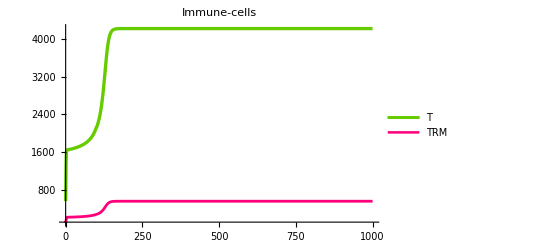

```mathematica
tCellVisualizer[highDcActNoRedWithTRMSol]
```

### Változtatások az előző verzióhoz képest (ezeket több lépésben adjuk majd hozzá):

- TRM nem hat a TNFalpha-ra ✓
- TRM apoptózis lassabb (aBaseLower) ✓
- T->TRM átmenet (3) és TRM limitáló faktor (4) függ az IL23-tól ✓
	*TRM termelődést serkenti
	*TRM kivonódást lassítja
-Differenciált keratinociták termelnek kis mennyiségű IL23-t (még nincs implementálva)
-IL23 blokkoló gyógyszer (drugIL23Red) (még nincs implementálva)

Tudjuk, hogy a TRM sejtek nem ugyanolyan arányban termelnek IL-17 és IL-22 citokineket mint a T-sejtek. “Ugyanezen cikk alapján a TRM-k magasabb arányban termelnek IL-17-t, mint a többi T sejt, viszont ugyanolyan arányban termeltek IL-22-t. ( nagyjából 2-szer jobban).”
A Reynolds modell ezeket azonban egyként kezeli, így ezt az arányt úgy oldjuk meg, hogy a T-sejtek IL-17/22 termelésének paraméterét szorozzuk egy 1 és 2 közötti számmal. 
(trm2il17Rate)

#### 1. IL23-tól NEM függő paraméterek

Új TRM egyenlet, citokinektől független t2trm, trm2t, trm20 paraméterekkel, ezek értékei véletlenszerűen választottak. (Az apoptózist és “kivonódást” is a T-sejteké felére állítjuk)

```mathematica
memoryTransferParameters=Append[stimulatedParameters,{t2trm->0.33, trm2t->0.002,trm20->0.5*1.51, aBaseLower->0.5*0.0036,trm2il17Rate->1.5}]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,t2trm→0.33,trm2t→0.002,trm20→0.755,aBaseLower→0.0018,trm2il17Rate→1.5|>

```mathematica
nonDependentMemoryEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20 *(SC[t])^p-aBase *SC[t],
TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta* SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase* DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20*DC[t]-aBase*DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*(T[t]+trm2il17Rate*TRM[t])-il1720*IL17⎵22[t],
T'[t]== t2*IL23[t]+trm2t*TRM[t]-t2trm*T[t]-t20*T[t]-aBase*T[t],
TRM'[t]==t2trm*T[t]-trm2t*TRM[t]-trm20*TRM[t]- aBaseLower*TRM[t],
GF'[t]== sc2gf*SC[t]+ta2gf*TA[t]-gf20*GF[t],
A'[t]== aBase*(SC[t]+TA[t]+DC[t]+T[t]+DK[t])+aBaseLower*TRM[t]-a20*A[t],
TNF'[t]== tnf2*T[t]-tnf20*TNF[t],
IL23'[t]== il232*DC[t]-il2320*IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 400, {il1722Red[t] -> il1722RedLater}]};
```

```mathematica
solveNonDependentMemory[parameterListM_,conditionListM_]:=
First[NDSolve[
Join[nonDependentMemoryEqns/.parameterListM, setInitialCondsWithTRM/.conditionListM],{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,1000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

Citokingátló gyógyszer nélkül:

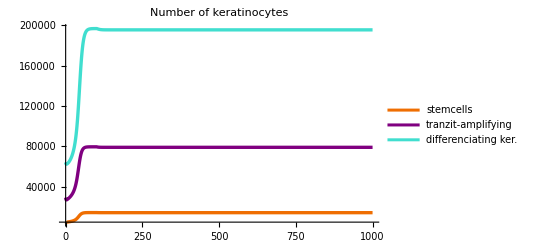
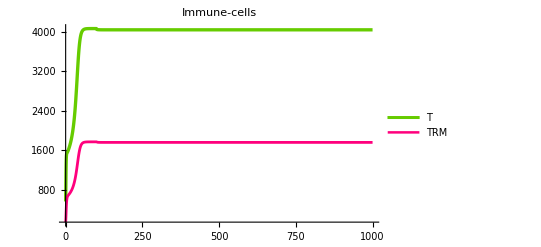

```mathematica
nonDependentMemoryTestSol=solveNonDependentMemory[memoryTransferParameters,initialCondsWithTRM];
Column[{visualizer[nonDependentMemoryTestSol],tCellVisualizer[nonDependentMemoryTestSol]}]
```

IL17/22 gátlóval, az IL17/22 blokkolva 30%-kal

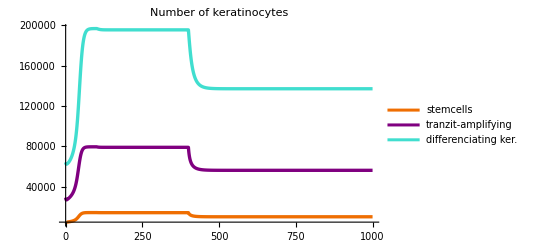
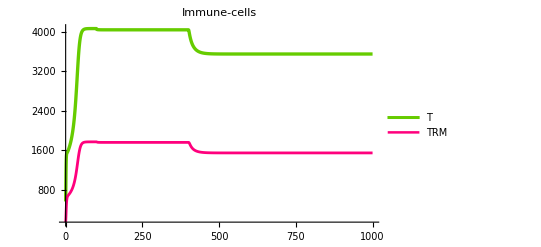

```mathematica
nonDependentMemoryWithReduction70Sol=solveNonDependentMemory[Append[memoryTransferParameters,{il1722RedLater->0.7,trm2il17Rate->1.5}],initialCondsWithTRM];
Column[{visualizer[nonDependentMemoryWithReduction70Sol],tCellVisualizer[nonDependentMemoryWithReduction70Sol]}]
```

#### 2. IL23-tól NEM függő, változtatható paraméterek (Manipulate)

Itt a trm2t és t2trm paramétereket lehet változtatni, hogy be tudjuk állítani az optimális T/TRM arányt.
Ez csak egy lehetőség a próbálgatásra.

```mathematica
manipulatedMemoryParameters=Append[stimulatedParameters,{trm20->0.5*1.51, aBaseLower->0.5*0.0036,trm2il17Rate->1.5}]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,trm20→0.755,aBaseLower→0.0018,trm2il17Rate→1.5|>

```mathematica
solveManipulatedMemory[parameterListM_,conditionListM_, trm2t0_,t2trm0_]:=First[NDSolve[Join[nonDependentMemoryEqns/.{Append[parameterListM,  {trm2t->trm2t0, t2trm->t2trm0}]}, setInitialCondsWithTRM/.conditionListM],{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,1000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

A TRM IL17/22 termelő rátája és IL17/22 gátló nélkül.

```mathematica
Manipulate[Module[{manipulatedTRMTest}, manipulatedTRMTest=solveManipulatedMemory[manipulatedMemoryParameters, initialCondsWithTRM,trm2t, t2trm];Column[{visualizer[manipulatedTRMTest],tCellVisualizer[manipulatedTRMTest]}]],{{trm2t,0.002},0,0.01,0.001,Appearance->"Labeled"},{{t2trm,0.2},0,1,0.01,Appearance->"Labeled"}, ContentSize->500];
```

#### 3. T->TRM függ az IL23-tól, többi konstans paraméter

Ebben a fejezetben bele akarunk illeszteni egy függvényt a T->TRM paraméter helyére. Ez egy monoton növő függvény, ami az IL23 transition egyensúlyi helyzeténél “ugrik” egyet. Ezzel azt szeretnénk elérni, hogy ha az IL23 átkerül a “beteg” tartományba, akkor a T->TRM átmenet megemelkedjen.
A többi paraméter továbbra is előre megadott és eltárolt érték.

```mathematica
regulatedTransferParameters=Append[stimulatedParameters,{trm2t->0.002, trm20->0.5*1.51, aBaseLower->0.5*0.0036, trm2il17Rate->1.5}]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,trm2t→0.002,trm20→0.755,aBaseLower→0.0018,trm2il17Rate→1.5|>

```mathematica
t2trmFunction[il23_]:=0.33+1/(1 + Exp[-(il23-52.20)])*0.33*0.5;
```

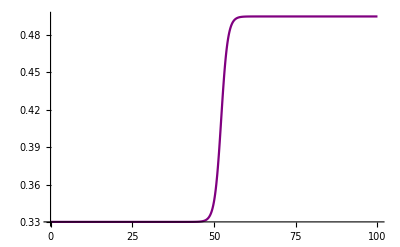

```mathematica
Plot[t2trmFunction[il23],{il23,0,100}, PlotStyle->Purple]
```

```mathematica
regulatedTransferMemoryEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20 *(SC[t])^p-aBase *SC[t],
TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta* SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase* DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20*DC[t]-aBase*DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*(T[t]+trm2il17Rate*TRM[t])-il1720*IL17⎵22[t],
T'[t]== t2*IL23[t]+trm2t*TRM[t]-t2trmFunction[IL23[t]]*T[t]-t20*T[t]-aBase*T[t],
TRM'[t]==t2trmFunction[IL23[t]]*T[t]-trm2t*TRM[t]-trm20*TRM[t]- aBaseLower*TRM[t],
GF'[t]== sc2gf*SC[t]+ta2gf*TA[t]-gf20*GF[t],
A'[t]== aBase*(SC[t]+TA[t]+DC[t]+T[t]+DK[t])+aBaseLower*TRM[t]-a20*A[t],
TNF'[t]== tnf2*T[t]-tnf20*TNF[t],
IL23'[t]== il232*DC[t]-il2320*IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 400, {il1722Red[t] -> il1722RedLater}]};
```

```mathematica
solveRegulatedTransferMemory[parameterListM_,conditionListM_]:=First[NDSolve[Join[regulatedTransferMemoryEqns/.parameterListM,setInitialCondsWithTRM/.conditionListM],{SC,TA,DK,DC,IL17⎵22,T,TRM, GF,A,TNF,IL23, dcActFunction, il1722Red},{t,0,1000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

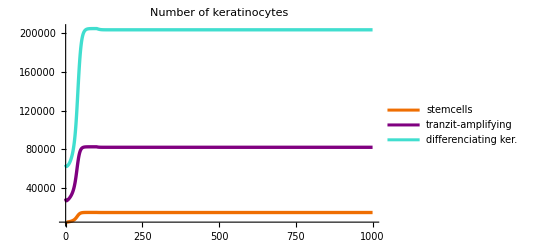
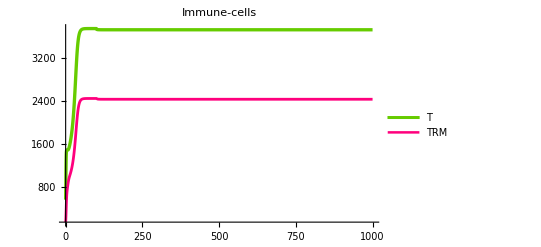

```mathematica
regulatedTransferMemoryTestSol=solveRegulatedTransferMemory[regulatedTransferParameters,initialCondsWithTRM];
Column[{visualizer[regulatedTransferMemoryTestSol],tCellVisualizer[regulatedTransferMemoryTestSol]}]
```

#### 4. T->TRM és TRM20 is függ IL23-tól

Ebben a fejezetben megpróbálunk a t2trm és a trm20 helyére is függvényt használni. Ami fontos, hogy míg a t2trm-et serkenti az IL23 szám, addig a trm20-ra gátlón hat, így ennek monoton csökkenő függvényt állítunk be.

```mathematica
fullyRegulatedParameters=Append[stimulatedParameters,{trm2t->0.002, aBaseLower->0.5*0.0036, trm2il17Rate->1.5}]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,trm2t→0.002,aBaseLower→0.0018,trm2il17Rate→1.5|>

```mathematica
trm20Function[il23_]:=fullyRegulatedParameters[t20]-1/(1 + Exp[-(il23-52.20)])*fullyRegulatedParameters[t20]*0.5;
```

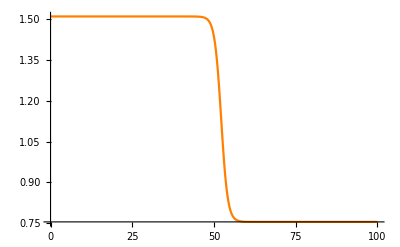

```mathematica
Plot[trm20Function[il23],{il23,0,100}, PlotStyle->Orange]
```

```mathematica
fullyRegulatedMemoryEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20 *(SC[t])^p-aBase *SC[t],
TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta* SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase* DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20*DC[t]-aBase*DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*(T[t]+trm2il17Rate*TRM[t])-il1720*IL17⎵22[t],
T'[t]== t2*IL23[t]+trm2t*TRM[t]-t2trmFunction[IL23[t]]*T[t]-t20*T[t]-aBase*T[t],
TRM'[t]==t2trmFunction[IL23[t]]*T[t]-trm2t*TRM[t]-trm20Function[IL23[t]]*TRM[t]- aBaseLower*TRM[t],
GF'[t]== sc2gf*SC[t]+ta2gf*TA[t]-gf20*GF[t],
A'[t]== aBase*(SC[t]+TA[t]+DC[t]+T[t]+DK[t])+aBaseLower*TRM[t]-a20*A[t],
TNF'[t]== tnf2*T[t]-tnf20*TNF[t],
IL23'[t]== il232*DC[t]-il2320*IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 400, {il1722Red[t] -> il1722RedLater}]};
```

```mathematica
solveFullyRegulatedMemory[parameterListM_,conditionListM_]:=First[NDSolve[Join[fullyRegulatedMemoryEqns/.parameterListM, setInitialCondsWithTRM/.conditionListM],{SC,TA,DK,DC,IL17⎵22,T,TRM, GF,A,TNF,IL23, dcActFunction, il1722Red},{t,0,1000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

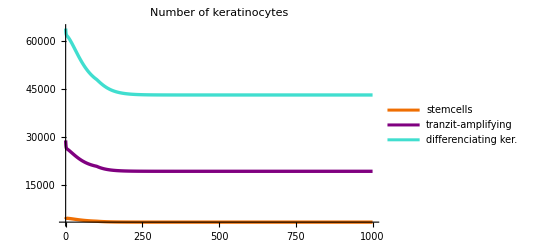
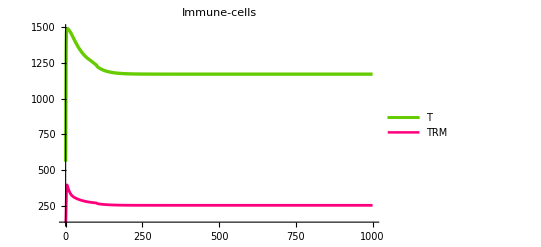

```mathematica
fullyRegulatedMemoryTestSol=solveFullyRegulatedMemory[fullyRegulatedParameters,initialCondsWithTRM];
Column[{visualizer[fullyRegulatedMemoryTestSol],tCellVisualizer[fullyRegulatedMemoryTestSol]}]
```

## Legkisebb négyzetek független paraméteres egyenletrendszerre (nonDependentMemoryEqns)

Korábban az egyenletrendszerbe újonnan bevezetett paramétereknek csak ötletszerűen adtunk meg értékeket. 
Szeretnénk most optimális értékeket keresni ezeknek, feltételezve, hogy a keratinociták viselkedése a Reynolds-modellben közel áll a valósághoz. Tehát a Reynolds-modell dcAct emelésével beteg egyensúlyhoz beállt megoldásgörbékhez szeretnénk illeszteni az új egyenletrendszer megoldását. Ezt a legkisebb négyzetek módszerével tesszük meg úgy, hogy figyelembe vesszük az ismereteinket a paraméterekről , és a TRM sejtek számáról.

Adatkinyerés egy görbéből:
Először az illesztéshez veszünk pontokat kis lépésenként.
Az ábrázoláshoz nagyobb lépésközzel veszünk pontokat, hogy ne folyjon össze.

```mathematica
originalData[function_,solution_]:=Table[function[t]/.solution,{t,0,300,0.2}]
```

```mathematica
dataToDraw[function_,solution_]:=Table[{t,function[t]/.solution},{t,0,300,3}]
```

Paraméteres megoldás:

```mathematica
parametricSol=ParametricNDSolve[
Join[nonDependentMemoryEqns/.stimulatedParameters, setInitialCondsWithTRM/.initialCondsWithTRM],{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,300},{t2trm,trm2t,trm20,aBaseLower,trm2il17Rate},DiscreteVariables->{dcActFunction, il1722Red}];
```

Adatkinyerés a paraméteres megoldásból:

```mathematica
estimatedData[function_,t_,t2trm_,trm2t_,trm20_,aBaseLower_,trm2il17Rate_]:=Table[function[t2trm,trm2t,trm20,aBaseLower,trm2il17Rate][t]/.parametricSol,{t,0,300,0.2}]
```

Úgy tudjuk, hogy a T-sejtek és a TRM-sejtek psoriasis-os bőrben ugyanannyian vannak, ezt igyekszünk elérni.
Adatkinyerés a T-TRM összehasonlításhoz (onnan ahol már beállt az egyensúly):

```mathematica
estimatedTcellData[function_,t2trm_,trm2t_,trm20_,aBaseLower_,trm2il17Rate_]:=Table[function[t2trm,trm2t,trm20,aBaseLower,trm2il17Rate][t]/.parametricSol,{t,200,201,0.2}]
```

```mathematica
estimatedTcellData[T,1.04562,0.0774399,1.36395,0.00279173,1.80864]
```

{2892.88,2892.88,2892.88,2892.88,2892.88,2892.89}

Célfüggvény:

```mathematica
leastSquaresObj[data1_,data2_]:=Total[(data1-data2)^2];
```

```mathematica
maxDistObj[tcell_,trm_]:=Max[Abs[tcell-trm]];
```

Optimalizálás a T-TRM egyenlőség feltétellel, majd az eredményünk ellenőrzéséhez ábrázolás:

```mathematica
optimalParams=NMinimize[{leastSquaresObj[originalData[SC,highDcActNoReductionSol],estimatedData[SC,t,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate]],t2trm>0,trm2t>0, t2trm>trm2t,0<trm20<1.51,0<aBaseLower<0.0036,trm2il17Rate>1,maxDistObj[estimatedTcellData[T,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate],estimatedTcellData[TRM,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate]]<20},{t2trm,trm2t,trm20,aBaseLower,trm2il17Rate}]
```

{1.33334×10^6,{t2trm→1.55922,trm2t→0.438269,trm20→1.12047,aBaseLower→0.000547957,trm2il17Rate→1.48836}}

```mathematica
optimizedTRMSol=First[NDSolve[
Join[Join[nonDependentMemoryEqns/.Append[stimulatedParameters,optimalParams[[2]]], setInitialCondsWithTRM/.initialCondsWithTRM]],{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,300},DiscreteVariables->{dcActFunction, il1722Red}]];
```

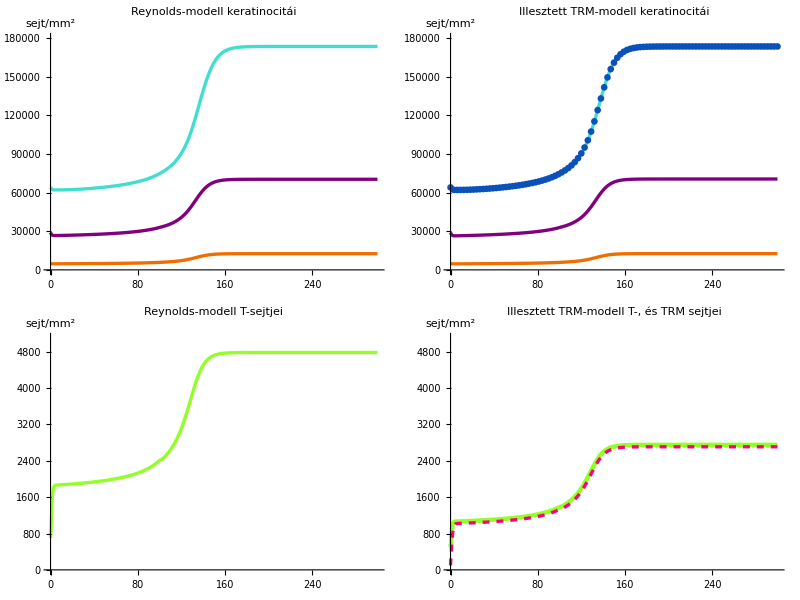

```mathematica
optimizedTRMPlot=Grid[{
{Plot[Evaluate[{SC[t],TA[t],DK[t]}/. highDcActNoReductionSol],{t,0,300},PlotStyle->{{RGBColor[0.937,0.431,0.008],Thickness[.006]},{RGBColor[0.5,0,0.5],Thickness[.006]},{RGBColor[0.25,0.87,0.81],Thickness[.006]}},ImageSize->Scaled[0.5],
PlotLabel->"Reynolds-modell keratinocitái", LabelStyle->Directive[Black,FontSize->17],AxesLabel->"sejt/mm^2",
(*PlotLegends->{"stemcells","tranzit-amplifying","differenciating ker."},*)PlotRange->{0,180000}],
Show[Plot[Evaluate[{SC[t],TA[t],DK[t]}/. optimizedTRMSol],{t,0,300},PlotStyle->{{RGBColor[0.937,0.431,0.008],Thickness[.006]},{RGBColor[0.5,0,0.5],Thickness[.006]},{RGBColor[0.25,0.87,0.81],Thickness[.006]}},ImageSize->Scaled[0.5],
PlotLabel->"Illesztett TRM-modell keratinocitái", LabelStyle->Directive[Black,FontSize->17],AxesLabel->"sejt/mm^2",
(*PlotLegends->{"stemcells","tranzit-amplifying","differenciating ker."},*)PlotRange->{0,180000}],
ListPlot[dataToDraw[DK,highDcActNoReductionSol],PlotStyle->Directive[PointSize[0.012],RGBColor[0.039,0.318,0.725]]]]},
{Plot[Evaluate[{T[t],TRM[t]}/. highDcActNoReductionSol],{t,0,300},PlotStyle->{{RGBColor[0.573,1.0,0.149],Thickness[.006]},{RGBColor[1,0,0.49],Thickness[.006]}},ImageSize->Scaled[0.5],
PlotLabel->"Reynolds-modell T-sejtjei", LabelStyle->Directive[Black,FontSize->17],AxesLabel->"sejt/mm^2",
(*PlotLegends->{"t-cells","trm"},*)PlotRange->{0,5100}],
Plot[Evaluate[{T[t],TRM[t]-42}/. optimizedTRMSol],{t,0,300},PlotStyle->{{RGBColor[0.573,1.0,0.149],Thickness[.008]},{RGBColor[1,0,0.49],Thickness[.006], Dashed}},ImageSize->Scaled[0.5],
PlotLabel->"Illesztett TRM-modell T-, és TRM sejtjei", LabelStyle->Directive[Black,FontSize->17],AxesLabel->"sejt/mm^2",
(*PlotLegends->{"t-cells","trm"},*)PlotRange->{0,5100}]}
(*{,SpanFromLeft,SwatchLegend[{RGBColor[1,0.64,0],RGBColor[0.5,0,0.5],RGBColor[0.25,0.87,0.81],RGBColor[0.4,0.8,0],RGBColor[1,0,0.49]},{"őssejtek","tranzit-amplifying","differenciált ker.","T-sejtek","TRM"}]}*)},Spacings->{2,2}]
```

Jelmagyarázat:

```mathematica
SwatchLegend[{RGBColor[0.937,0.431,0.008],RGBColor[0.5,0,0.5],RGBColor[0.25,0.87,0.81],RGBColor[0.573,1.0,0.149],RGBColor[1,0,0.49]},{"őssejtek","tranzit-amplifying","differenciált ker.","T-sejtek","TRM"}]
```

```mathematica
SwatchLegend[{RGBColor[0.937,0.431,0.008],RGBColor[0.5,0,0.5],RGBColor[0.25,0.87,0.81]},{"őssejtek","tranzit-amplifying","differenciált ker."}]
```

### Constraint vs célfüggvény

Felmerült a kérdés, hogy a constraint-es (C) vagy  célfüggvényes (F) megoldás jobb a T-TRM arány megszorításához.
A C esetben az optimalizálásnál feltételnek betesszük, hogy a kapott paraméterekkel a T és TRM görbék távolsága legfeljebb az értékük kb. 1%-a.
Az F esetben a célfüggvényben a keratinociták távolságának négyzetösszegén kívül szerepel a T és TRM távolságának négyzetösszege is, kisebb súllyal.
Kiszámoljuk mindkettővel, és összehasonlítjuk az eredményeket.

```mathematica
c=NMinimize[{leastSquaresObj[originalData[SC,highDcActNoReductionSol],estimatedData[SC,t,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate]],t2trm>0,trm2t>0, t2trm>trm2t,0<trm20<1.51,0<aBaseLower<0.0036,trm2il17Rate>1,maxDistObj[estimatedTcellData[T,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate],estimatedTcellData[TRM,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate]]<20},{t2trm,trm2t,trm20,aBaseLower,trm2il17Rate}]
```

{1.33334×10^6,{t2trm→1.55922,trm2t→0.438269,trm20→1.12047,aBaseLower→0.000547957,trm2il17Rate→1.48836}}

```mathematica
f=NMinimize[{leastSquaresObj[originalData[SC,highDcActNoReductionSol],estimatedData[SC,t,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate]]+0.4*leastSquaresObj[estimatedTcellData[T,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate],estimatedTcellData[TRM,t2trm,trm2t,trm20,aBaseLower,trm2il17Rate]],t2trm>0,trm2t>0, t2trm>trm2t,0<trm20<1.51,0<aBaseLower<0.0036,trm2il17Rate>1},{t2trm,trm2t,trm20,aBaseLower,trm2il17Rate}]
```

{805871.,{t2trm→1.18188,trm2t→0.0999672,trm20→1.22409,aBaseLower→0.00253335,trm2il17Rate→1.62602}}

A trm20, aBaseLower és trm2il17Rate a két módszerrel hasonló értéket kap.
A t2trm és trm2t-re kapott két érték között ellenőrizzük a függvény viselkedését. A cél ezzel az, hogy ellenőrizzük, hogy a két érték közt nem száll el, és ha nincs probléma, akkor a két módszer közül mindegy melyiket használjuk.

```mathematica
Manipulate[Module[{manipulatedTRMTest}, manipulatedTRMTest=solveManipulatedMemory[Append[stimulatedParameters,{c[[2]][[3]],c[[2]][[4]],c[[2]][[5]]}], initialCondsWithTRM,trm2t, t2trm];Column[{visualizer[manipulatedTRMTest],tCellVisualizer[manipulatedTRMTest]}]],{{trm2t,0.09996863726867762},0.09996863726867762,0.43826910065931945,Appearance->"Labeled"},{{t2trm,1.1818847474843248},1.1818847474843248,1.5592204124233504,Appearance->"Labeled"}, ContentSize->500];
```

Azt látjuk,  hogy a megoldások nem szállnak el, a paraméterek változtatása csak a T-TRM arányt változtatja. (Tehát mindegy melyik módszert használjuk, továbbmehetünk az optimalParams-szal)

### A TRM-es modell egyensúlyi helyzetei

Az egyensúlyi helyzetek kiszámolásához szükségünk lesz a paraméterekre, illetve a korábban bevezetett WhenEvent-es függvényeknek is adni kell egy értéket.

```mathematica
steadyTRMparam=Append[Append[primaryParameters,{il1722Red->1,dcAct0->1880*1.02}],optimalParams[[2]]]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722Red→1,dcAct0→1917.6,t2trm→1.55922,trm2t→0.438269,trm20→1.12047,aBaseLower→0.000547957,trm2il17Rate→1.48836|>

```mathematica
trmSteadyStateEqns[params_]:=Solve[{0==sc2 *(IL17⎵22+TNF)*SC-sc20 *(SC)^p-aBase *SC,
0==(IL17⎵22+TNF)*(sc2ta* SC+ta2 *TA)-ta20 *(TA)^p-aBase *TA,
0==ta2d *(IL17⎵22+TNF)*TA-d20 *(DK)^p-aBase* DK-dDesq *DK,
0== (dcVm*(GF)^n)/(dcKp+(GF)^n)+dcAct-dc20*DC-aBase*DC,
0== il172 *il1722Red*(T+trm2il17Rate*TRM)-il1720*IL17⎵22,
0== t2*IL23+trm2t*TRM-t2trm*T-t20*T-aBase*T,
0==t2trm*T-trm2t*TRM-trm20*TRM- aBaseLower*TRM,
0== sc2gf*SC+ta2gf*TA-gf20*GF,
0== aBase*(SC+TA+DC+T+DK)+aBaseLower*TRM-a20*A,
0== tnf2*T-tnf20*TNF,
0== il232*DC-il2320*IL23}/.params,{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23}]
```

A Reynolds-modellhez hasonlóan megnézzük, hogy hány egyensúlyi helyzete van és ezek milyenek.

```mathematica
Length[trmSteadyStateEqns[steadyTRMparam]]
```

32

Valósak:

```mathematica
steadyTRM=realSteadyStates[trmSteadyStateEqns[steadyTRMparam]]
```

{<|SC→3989.59,TA→22461.6,DK→51131.6,DC→1575.83,IL17⎵22→30.7219,T→901.299,TRM→901.259,GF→724.689,A→8.0197,TNF→12.3466,IL23→43.1734|>,<|SC→4802.26,TA→27010.9,DK→62700.2,DC→1881.61,IL17⎵22→36.6832,T→1076.19,TRM→1076.14,GF→871.593,A→9.76349,TNF→14.7423,IL23→51.5509|>,<|SC→12581.5,TA→70558.4,DK→174039.,DC→4808.66,IL17⎵22→93.7482,T→2750.32,TRM→2750.2,GF→2277.81,A→26.5156,TNF→37.6757,IL23→131.744|>}

Értékek kigyűjtése:

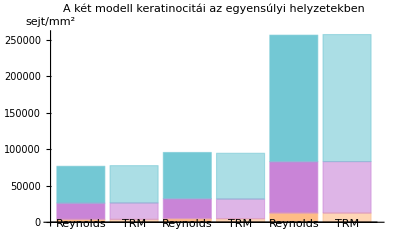

```mathematica
BarChart[{Labeled[{SC,TA,DK}/.steadyKeratinocytes[[1]],"Reynolds"],Style[Labeled[{SC,TA,DK}/.steadyTRM[[1]],"TRM"],Opacity[0.6]],
Labeled[{SC,TA,DK}/.steadyKeratinocytes[[2]],"Reynolds"],Style[Labeled[{SC,TA,DK}/.steadyTRM[[2]],"TRM"],Opacity[0.6]],
Labeled[{SC,TA,DK}/.steadyKeratinocytes[[3]],"Reynolds"],Style[Labeled[{SC,TA,DK}/.steadyTRM[[3]],"TRM"],Opacity[0.6]]},
ChartLayout->"Stacked",ChartStyle->{{RGBColor[0.996,0.737,0.522],RGBColor[0.788,0.518,0.843],RGBColor[0.451,0.784,0.831]}}, AxesLabel->"sejt/mm^2",ImageSize->Scaled[0.5],PlotLabel->"A két modell keratinocitái az egyensúlyi helyzetekben", LabelStyle->Directive[Black,FontSize->12]]
```

```mathematica
Grid[{{BarChart[{Labeled[{SC,TA,DK}/.steadyKeratinocytes[[1]],"healthy"],Labeled[{SC,TA,DK}/.steadyKeratinocytes[[2]],"transition"],Labeled[{SC,TA,DK}/.steadyKeratinocytes[[3]],"psoriatic"]}, ChartLayout->"Stacked",LabelingFunction->Center,ChartStyle->{{RGBColor[0.996,0.737,0.522],RGBColor[0.788,0.518,0.843],RGBColor[0.451,0.784,0.831]}},ImageSize->Scaled[0.5],PlotLabel->"Keratinociták a Reynolds egyensúlyi helyzetekben"],BarChart[{Labeled[{SC,TA,DK}/.steadyTRM[[1]],"healthy"],Labeled[{SC,TA,DK}/.steadyTRM[[2]],"transition"],Labeled[{SC,TA,DK}/.steadyTRM[[3]],"psoriatic"]}, ChartLayout->"Stacked",LabelingFunction->Center,ChartStyle->{{RGBColor[0.996,0.737,0.522],RGBColor[0.788,0.518,0.843],RGBColor[0.451,0.784,0.831]}},ImageSize->Scaled[0.5],PlotLabel->"Keratinociták a TRM-es egyensúlyi helyzeteiben"]}}];
```

### DcAct vizsgálata az új paraméterekkel, és a visszatérés ellenőrzése

A TRM bevételének azért van jelentősége, mert a memória T-sejtek az immunrendszer túlműködése alatt kialakulnak, és később amik minden visszaáll a normálisba, akkor is megmaradnak. Ez elősegíti a psoriasis fellángolását, a TRM-ek jelenléte könnyen újra beindíthatja a folyamatot.
Azt szeretnénk elérni, hogy a betegség visszatérjen olyan esetben is amikor a Reynolds-ban nem ✓

A paraméterek és kezdeti értékek amiket használunk:

```mathematica
newParameters=Append[stimulatedParameters,optimalParams[[2]]]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,t2trm→1.55922,trm2t→0.438269,trm20→1.12047,aBaseLower→0.000547957,trm2il17Rate→1.48836|>

```mathematica
initialCondsWithTRM
```

<|sc0→5000,ta0→29000,dk0→64000,dc0→700,a0→2,il170→20,il230→40,tnf0→20,gf0→700,dcAct0→1917.6,trm0→140,t0→560|>

“Egészséges”, alacsony dcAct:

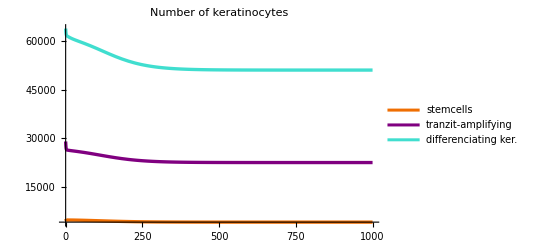

```mathematica
healthyInitLowDcActTRMSol=solveNonDependentMemory[newParameters,Append[initialCondsWithTRM,dcAct0->1880]];
visualizer[healthyInitLowDcActTRMSol]
```

magas kezdeti érték:

```mathematica
initialConditionsPsoriTRM=<|sc0->6000,ta0->35000,dk0->80000,t0->1840,trm0->460,dc0->2300,a0->6,il170->60,il230->40,tnf0->60,gf0->2100,dcAct0->1880|>;
```

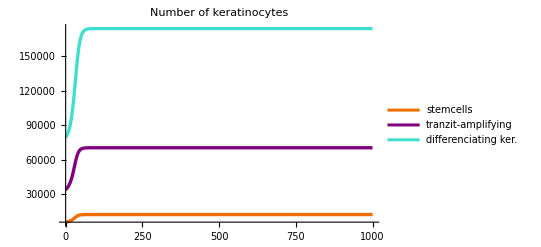

```mathematica
psoriInitLowDcActTRMSol=solveNonDependentMemory[newParameters,initialConditionsPsoriTRM];
visualizer[psoriInitLowDcActTRMSol]
```

2%-kal megemelt dcAct:

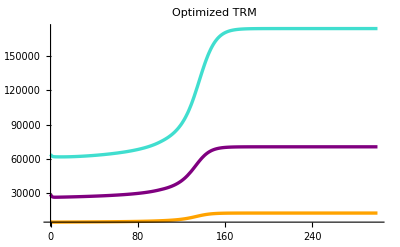
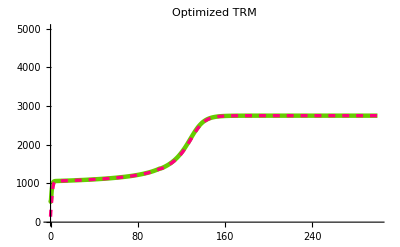
-Graphics- | -Graphics-
 |

```mathematica
highDcActTRMSol=solveNonDependentMemory[newParameters,initialCondsWithTRM];
trmVisualizer[highDcActTRMSol]
```

Megemelt dcAct és citokingátlás:
Ebben a citokinblokkoló 30%-os, ez korábban visszaállította a Reynolds-t az egészséges egyensúlyi helyzet környékére (lásd. DcAct vizsgálat)

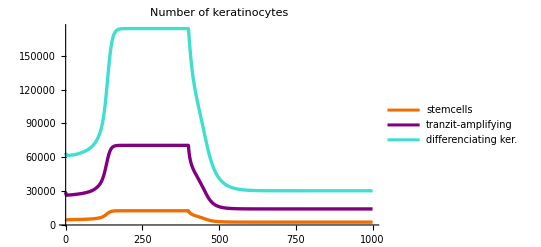

```mathematica
highDcActTRMRed70=solveNonDependentMemory[Append[newParameters,il1722RedLater->0.7],initialCondsWithTRM];
visualizer[highDcActTRMRed70]
```

A betegség visszatérését úgy fogjuk kipróbálni, hogy vesszük a TRM értékét a betegség kialakulása után, és ezt írjuk az egészséges kezdeti értékek közé. Azt próbáljuk ezzel szimulálni, hogy miután egy psoriasis “hullám” lecsengett és a bőr visszaállt normális állapotába, a TRM szám attól magas maradt, mert a TRM sejtek megmaradnak. Ezekkel a kezdeti értékekkel, a dcAct megemelése nélkül végzünk szimulációt, hogy megnézzük inger nélkül előjön-e a betegség.

```mathematica
newTRM=TRM[250]/.highDcActTRMSol
```

2750.2

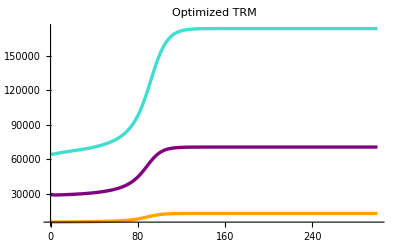
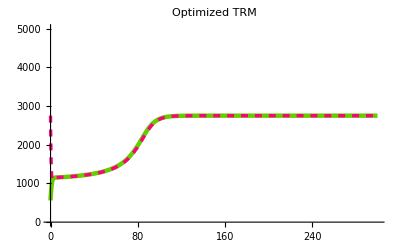
-Graphics- | -Graphics-
 |

```mathematica
relapse=solveNonDependentMemory[newParameters,Append[initialCondsWithTRM,{trm0->newTRM,dcAct0->1880}]];
trmVisualizer[relapse]
```

Előjön a betegség alacsony dcAct ellenére, azaz immunológiai inger nélkül.

## Gyógyítás

A TRM-modell is gyógyítható, méghozzá kisebb csökkentéssel és kevesebb idő alatt.

```mathematica
newVisualizer[solution_]:= Plot[Evaluate[{SC[t],TA[t],DK[t]}/. solution],{t,0,2000},PlotStyle->{{RGBColor[0.937,0.431,0.008],Thickness[.006]},{RGBColor[0.5,0,0.5],Thickness[.006]},{RGBColor[0.25,0.87,0.81],Thickness[.006]}},ImageSize->Scaled[0.5],AxesLabel->"sejt/mm^2",
PlotLabel->"Keratinociták száma", LabelStyle->Directive[Black,FontSize->17],PlotRange->All];
```

```mathematica
initialCondsWithMed=Append[initialConditionsHealthy,dcAct0->1880]
```

<|sc0→5000,ta0→29000,dk0→64000,t0→700,dc0→700,a0→2,il170→20,il230→40,tnf0→20,gf0→700,dcAct0→1880|>

```mathematica
stimulatedParameters=Append[primaryParameters, {il1722RedLater->1,dcActLater->1880*1.02}]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,dcActLater→1917.6|>

### IL17 gátló a Reynolds-modellben örökké

Gyógyszer adás nélkül:

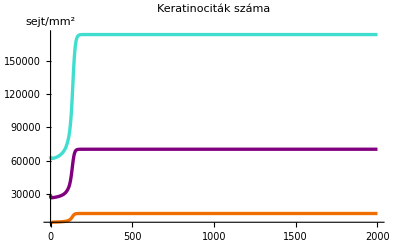

```mathematica
newVisualizer[highDcActNoReductionSol]
```

Ez alapján állítjuk be a WhenEvent-et a gyógyszeradagoláshoz.

```mathematica
reynoldsWithMedForeverEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20*(SC[t])^p-aBase *SC[t],TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta *SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase *DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20 *DC[t]-aBase *DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*T[t]-il1720* IL17⎵22[t],
T'[t]== t2 *IL23[t]-t20* T[t]-aBase* T[t],
GF'[t]== sc2gf* SC[t]+ta2gf *TA[t]-gf20* GF[t],
A'[t]== aBase *(SC[t]+TA[t]+DC[t]+T[t]+DK[t])-a20* A[t],
TNF'[t]== tnf2* T[t]-tnf20*TNF[t],
IL23'[t]== il232 *DC[t]-il2320 *IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcActLater}],
WhenEvent[t == 310, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 600, {il1722Red[t] -> il1722RedLater}]};
```

Ha később van az immunológiai inger, akkor hosszabb ideig van rá szükség a betegség kialakulásához. A kezdeti egészséges dcAct miatt először elkezd az egészséges egyensúlyi helyzethez közelíteni. 
A gyógyszeradagolás kezdetét t=600-ra tettem, ott már látszik, hogy kialakult a betegség a kezelés előtt.

```mathematica
solveReynoldsWithMedForever[parameterListR_,conditionListR_]:=First[NDSolve[
Join[reynoldsWithMedForeverEqns/.parameterListR, setInitialCondsStimulated/.conditionListR],{SC,TA,DK,DC,IL17⎵22,T,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,2000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

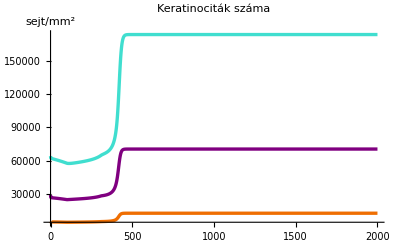

```mathematica
newVisualizer[solveReynoldsWithMedForever[Append[stimulatedParameters,il1722RedLater->1],initialCondsWithMed]]
```

Alacsonyabbra áll be mint az eredeti egészséges egyensúlyi helyzet

### IL17 gátló a Reynolds-modellben egy ideig

```mathematica
reynoldsWithMedSomeTimeEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20*(SC[t])^p-aBase *SC[t],TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta *SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase *DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20 *DC[t]-aBase *DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*T[t]-il1720* IL17⎵22[t],
T'[t]== t2 *IL23[t]-t20* T[t]-aBase* T[t],
GF'[t]== sc2gf* SC[t]+ta2gf *TA[t]-gf20* GF[t],
A'[t]== aBase *(SC[t]+TA[t]+DC[t]+T[t]+DK[t])-a20* A[t],
TNF'[t]== tnf2* T[t]-tnf20*TNF[t],
IL23'[t]== il232 *DC[t]-il2320 *IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcActLater}],
WhenEvent[t == 290, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 600, {il1722Red[t] -> il1722RedLater}],
WhenEvent[t == 1112, {il1722Red[t] -> 1}]};
```

```mathematica
solveReynoldsWithMedSomeTime[parameterListR_,conditionListR_]:=First[NDSolve[
Join[reynoldsWithMedSomeTimeEqns/.parameterListR, setInitialCondsStimulated/.conditionListR],{SC,TA,DK,DC,IL17⎵22,T,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,2000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

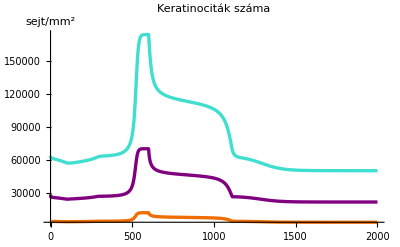

```mathematica
newVisualizer[solveReynoldsWithMedSomeTime[Append[stimulatedParameters,il1722RedLater->0.71],initialCondsWithMed]]
```

Így a korábban is ismert egészséges egyensúlyi helyzethez áll be.

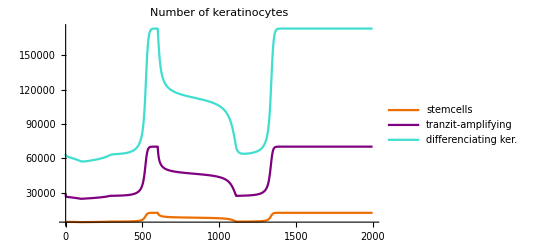
t=1111esetén még visszatér: -Graphics-

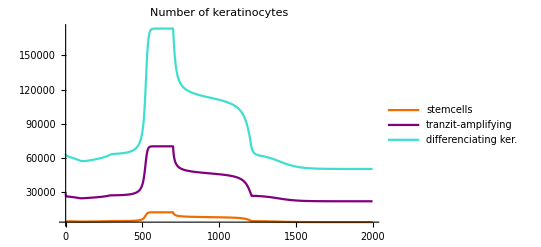
Tehát 512 időegységig adva a citokingátlót, elérjük az egészséges állapotot. Ezt kipróbáltam 700-1212-vel is: 
-Graphics-

### IL17 gátló a TRM-es modellben örökké

Gyógyszer nélkül:

```mathematica
trmParameters=Append[stimulatedParameters,optimalParams[[2]]]
```

<|sc2→0.0017635,sc20→0.000018135,sc2ta→0.0015415,sc2gf→1,ta2→0.0017562,ta20→3.7321×10^-6,ta2d→0.0018063,ta2gf→1,d20→5.05×10^-7,dDesq→0.0047529,dc20→1.51,dcVm→6000,dcKp→3000000000000,il172→0.5,il1720→36.5,t2→55,t20→1.51,gf20→36.5,aBase→0.0036,a20→36,tnf2→0.5,tnf20→36.5,il232→1,il2320→36.5,p→2,n→4,dcAct→1880,il1722RedLater→1,dcActLater→1917.6,t2trm→1.55922,trm2t→0.438269,trm20→1.12047,aBaseLower→0.000547957,trm2il17Rate→1.48836|>

```mathematica
initialCondsWithMedTRM=Append[initialCondsWithTRM,dcAct0->1880]
```

<|sc0→5000,ta0→29000,dk0→64000,dc0→700,a0→2,il170→20,il230→40,tnf0→20,gf0→700,trm0→140,t0→560,dcAct0→1880|>

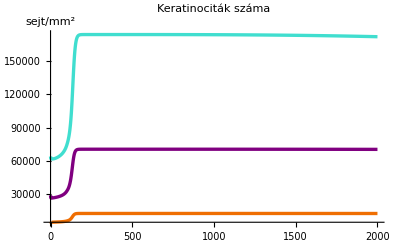

```mathematica
newVisualizer[optimizedTRMSol]
```

```mathematica
memoryWithMedForeverEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20 *(SC[t])^p-aBase *SC[t],
TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta* SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase* DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20*DC[t]-aBase*DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*(T[t]+trm2il17Rate*TRM[t])-il1720*IL17⎵22[t],
T'[t]== t2*IL23[t]+trm2t*TRM[t]-t2trm*T[t]-t20*T[t]-aBase*T[t],
TRM'[t]==t2trm*T[t]-trm2t*TRM[t]-trm20*TRM[t]- aBaseLower*TRM[t],
GF'[t]== sc2gf*SC[t]+ta2gf*TA[t]-gf20*GF[t],
A'[t]== aBase*(SC[t]+TA[t]+DC[t]+T[t]+DK[t])+aBaseLower*TRM[t]-a20*A[t],
TNF'[t]== tnf2*T[t]-tnf20*TNF[t],
IL23'[t]== il232*DC[t]-il2320*IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcActLater}],
WhenEvent[t == 290, {dcActFunction[t] -> dcAct}],
WhenEvent[t == 600, {il1722Red[t] -> il1722RedLater}]};
```

```mathematica
solvememoryWithMedForever[parameterListM_,conditionListM_]:=
First[NDSolve[
Join[memoryWithMedForeverEqns/.parameterListM, setInitialCondsWithTRM/.conditionListM],{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,2000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

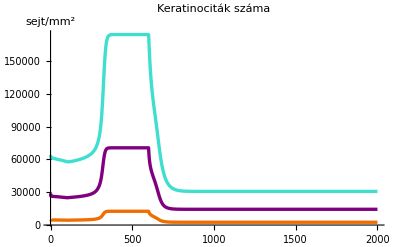

```mathematica
newVisualizer[solvememoryWithMedForever[Append[trmParameters, il1722RedLater->0.71],initialCondsWithMedTRM]]
```

A Reynoldshoz képest kisebb csökkentéssel az egészséges egyensúlyhoz közel vihető:

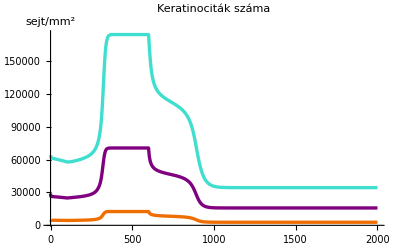

```mathematica
newVisualizer[solvememoryWithMedForever[Append[trmParameters, il1722RedLater->0.79],initialCondsWithMedTRM]]
```

```mathematica
newVisualizer[solvememoryWithMedForever[Append[trmParameters, il1722RedLater->0.79],initialCondsWithMedTRM]]
```

-Graphics-

### IL17 gátló a TRM-es modellben egy ideig

```mathematica
memoryWithMedSomeTimeEqns={SC'[t]==sc2 *(IL17⎵22[t]+TNF[t])*SC[t]-sc20 *(SC[t])^p-aBase *SC[t],
TA'[t]==(IL17⎵22[t]+TNF[t])*(sc2ta* SC[t]+ta2 *TA[t])-ta20 *(TA[t])^p-aBase *TA[t],
DK'[t]==ta2d *(IL17⎵22[t]+TNF[t])*TA[t]-d20 *(DK[t])^p-aBase* DK[t]-dDesq *DK[t],
DC'[t]== (dcVm*(GF[t])^n)/(dcKp+(GF[t])^n)+dcActFunction[t]-dc20*DC[t]-aBase*DC[t],
IL17⎵22'[t]== il172 *il1722Red[t]*(T[t]+trm2il17Rate*TRM[t])-il1720*IL17⎵22[t],
T'[t]== t2*IL23[t]+trm2t*TRM[t]-t2trm*T[t]-t20*T[t]-aBase*T[t],
TRM'[t]==t2trm*T[t]-trm2t*TRM[t]-trm20*TRM[t]- aBaseLower*TRM[t],
GF'[t]== sc2gf*SC[t]+ta2gf*TA[t]-gf20*GF[t],
A'[t]== aBase*(SC[t]+TA[t]+DC[t]+T[t]+DK[t])+aBaseLower*TRM[t]-a20*A[t],
TNF'[t]== tnf2*T[t]-tnf20*TNF[t],
IL23'[t]== il232*DC[t]-il2320*IL23[t],
WhenEvent[t == 100, {dcActFunction[t] -> dcActLater}],
WhenEvent[t == 290, {dcActFunction[t] -> dcAct}],
WhenEvent[t ==600, {il1722Red[t] -> il1722RedLater}],
WhenEvent[t ==895, {il1722Red[t]->1}]};
```

```mathematica
solvememoryWithMedSomeTime[parameterListM_,conditionListM_]:=
First[NDSolve[
Join[memoryWithMedSomeTimeEqns/.parameterListM, setInitialCondsWithTRM/.conditionListM],{SC,TA,DK,DC,IL17⎵22,T,TRM,GF,A,TNF,IL23,dcActFunction, il1722Red},{t,0,2000},DiscreteVariables->{dcActFunction, il1722Red}]];
```

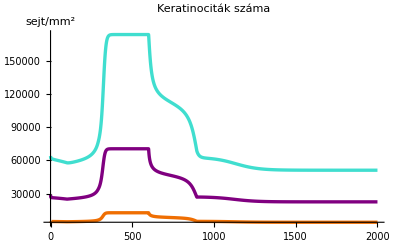

```mathematica
newVisualizer[solvememoryWithMedSomeTime[Append[trmParameters, il1722RedLater->0.79],initialCondsWithMedTRM]]
```

```mathematica
trmMedSol=solvememoryWithMedSomeTime[Append[trmParameters, il1722RedLater->0.79],initialCondsWithMedTRM];
```

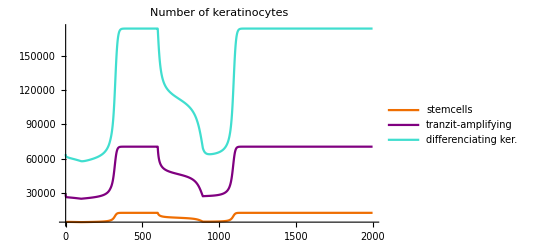
t=894 esetén:-Graphics-

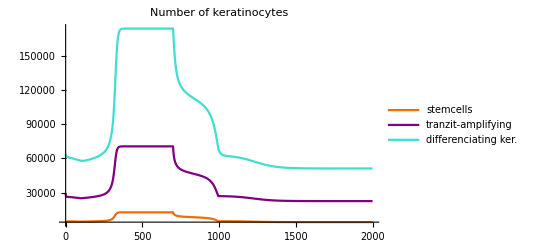
295 időegység alatt elérjük az egészséges állapotot. Ezt kipróbáltam 700-995-ig 
-Graphics-

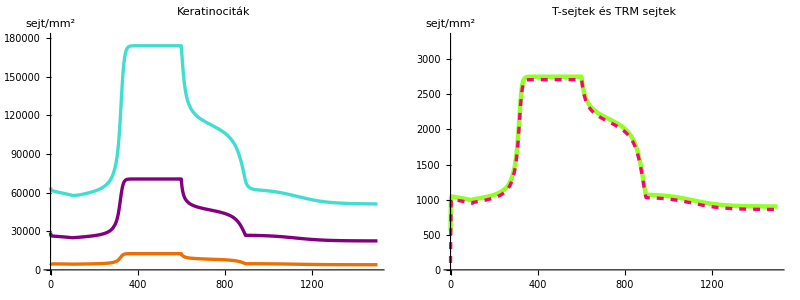

```mathematica
Grid[{{Plot[Evaluate[{SC[t],TA[t],DK[t]}/. trmMedSol],{t,0,1500},PlotStyle->{{RGBColor[0.937,0.431,0.008],Thickness[.006]},{RGBColor[0.5,0,0.5],Thickness[.006]},{RGBColor[0.25,0.87,0.81],Thickness[.006]}},ImageSize->Scaled[0.5],AxesLabel->"sejt/mm^2",
PlotLabel->"Keratinociták", LabelStyle->Directive[Black,FontSize->15],
(*PlotLegends->{"stemcells","tranzit-amplifying","differenciating ker."},*)PlotRange->{0,180000}],Plot[Evaluate[{T[t],TRM[t]-42}/. trmMedSol],{t,0,1500},PlotStyle->{{RGBColor[0.573,1.0,0.149],Thickness[.008]},{RGBColor[1,0,0.49],Thickness[.006], Dashed}},ImageSize->Scaled[0.5],AxesLabel->"sejt/mm^2",
PlotLabel->"T-sejtek és TRM sejtek", LabelStyle->Directive[Black,FontSize->15],
(*PlotLegends->{"t-cells","trm"},*)PlotRange->{0,3300}]}},Spacings->{2,2}]
```